# PCET in the inverted region--Modeling

## Zachary K. Goldsmith Copyright 2005-2013 Hammes-Schiffer Group, University of Illinois at Urbana-Champaign; (Alexander Soudackov, Brian Solis, Samantha Horvath, Ben Auer)

```mathematica
ClearAll["Global`*"]
```

Change to the directory containing this notebook:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Zach/inverted-region-model

Include all the function from the MathPCETwithET package (must be in the same directory):

```mathematica
Needs["MathPCET`"]
```

```mathematica
?MorseWavefunctionRight
```

MorseWavefunctionRight[n,Beta,DE,x]
Returns wavefunction for the mirrored Morse oscillator in units of (Bohr)^(-1/2).
Parameters:
n = 0, 1, 2,... - quantum number,
Beta - Morse parameter (in 1/Bohr),
DE - dissociation energy (in kcal/mol),
x - coordinate (in Bohrs) relative to the minimum of the potential.
Options:
M -> mass of the particle in Daltons (Default - mass of the proton).

## Conversion factors

```mathematica
a2m=10^-10;
m2a=10^10;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
kg2amu=1.660539`10*10^-27;
debye2Cm = 3.33564*10^(-30);
```

## Parameters

```mathematica
TT=298.15; (* Temperature in K *)
Vel=1.0; (* Electronic coupling in kcal/mol (does not affect KIE) *)
λs=1.40 ev2kcal (* Total reorganization energy in kcal/mol - should be determined separately *)
dGc=-2.53619 ev2kcal ;     (*Delta G of recombination in eV, charge-CDFT *)
ngrid=256;
nstates=12;
```

32.2849

## R-dependences of P(R)

Effective force constant for donor-acceptor motion
and equilibrium donor-acceptor distance (in Å)

```mathematica
kaeff=0.051199377;
kceff=0.051628643;
keff=0.5*(kaeff+kceff);
Rav0=0.5*(2.56592+2.56513)*a2bohr;
Ωav=Sqrt[(2.0*π*kb*TT)/keff]*bohr2a;
```

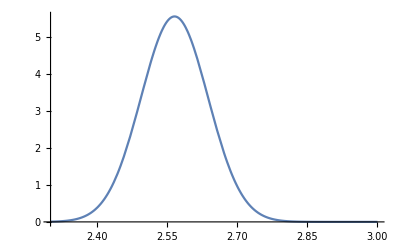

```mathematica
Pav[R_]=Exp[-(0.5*keff*(R*a2bohr-Rav0)^2)/(kb*TT)]/Ωav;
Plot[Pav[R],{R,2.3,3.0},PlotRange->All]
```

Check normalization:

```mathematica
NIntegrate[Pav[R],{R,-∞,∞}]
```

1.

```mathematica
keff
```

0.051414

## R (O-N) distances (Å)

Donor-Acceptor Distances:

```mathematica
R237=2.36553;
R242=2.41553;
R247=2.46553;
R252=2.51553;
R257=2.56553;
R262=2.61553;
R267=2.66553;
R272=2.71553;
R277=2.76553;
R282=2.81553;
R287=2.86553;
```

## Reactant (1a) and product (2b) wavefunctions

Calculate vibrational states for all PT profiles (take a bit of time):
(Note that the package settings assume that the executable fgh_bspline.bin is found in /usr/local/bspline/bin)

```mathematica
Test237=FGHWavefunctionsZach["06_d236_pes.dat",64,5];
```

```mathematica
waveH237=FGHWavefunctions["06_d236_pes.dat",ngrid,nstates];
waveH242=FGHWavefunctions["06_d241_pes.dat",ngrid,nstates];
waveH247=FGHWavefunctions["06_d246_pes.dat",ngrid,nstates];
waveH252=FGHWavefunctions["06_d251_pes.dat",ngrid,nstates];
waveH257=FGHWavefunctions["06_d256_pes.dat",ngrid,nstates];
waveH262=FGHWavefunctions["06_d261_pes.dat",ngrid,nstates];
waveH267=FGHWavefunctions["06_d266_pes.dat",ngrid,nstates];
waveH272=FGHWavefunctions["06_d271_pes.dat",ngrid,nstates];
waveH277=FGHWavefunctions["06_d276_pes.dat",ngrid,nstates];
waveH282=FGHWavefunctions["06_d281_pes.dat",ngrid,nstates];
waveH287=FGHWavefunctions["06_d286_pes.dat",ngrid,nstates];
```

```mathematica
waveD237=FGHWavefunctions["06_d236_pes.dat",ngrid,nstates,M->MassD];
waveD242=FGHWavefunctions["06_d241_pes.dat",ngrid,nstates,M->MassD];
waveD247=FGHWavefunctions["06_d246_pes.dat",ngrid,nstates,M->MassD];
waveD252=FGHWavefunctions["06_d251_pes.dat",ngrid,nstates,M->MassD];
waveD257=FGHWavefunctions["06_d256_pes.dat",ngrid,nstates,M->MassD];
waveD262=FGHWavefunctions["06_d261_pes.dat",ngrid,nstates,M->MassD];
waveD267=FGHWavefunctions["06_d266_pes.dat",ngrid,nstates,M->MassD];
waveD272=FGHWavefunctions["06_d271_pes.dat",ngrid,nstates,M->MassD];
waveD277=FGHWavefunctions["06_d276_pes.dat",ngrid,nstates,M->MassD];
waveD282=FGHWavefunctions["06_d281_pes.dat",ngrid,nstates,M->MassD];
waveD287=FGHWavefunctions["06_d286_pes.dat",ngrid,nstates,M->MassD];
```

Check (visualize) the wavefunctions:

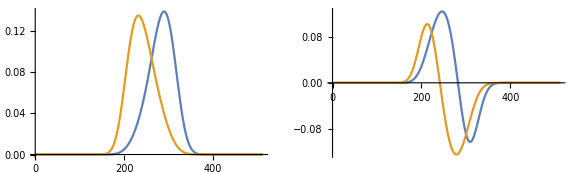

```mathematica
GraphicsRow[
{ListLinePlot[{waveH237⟦1,3,1⟧,waveH237⟦2,3,1⟧},PlotRange->All],ListLinePlot[{waveH237⟦1,3,2⟧,waveH237⟦2,3,2⟧},PlotRange->All]},
ImageSize->Large
]
```

```mathematica
WaveH237
```

WaveH237

More elaborate plots for checking that everything makes sense:

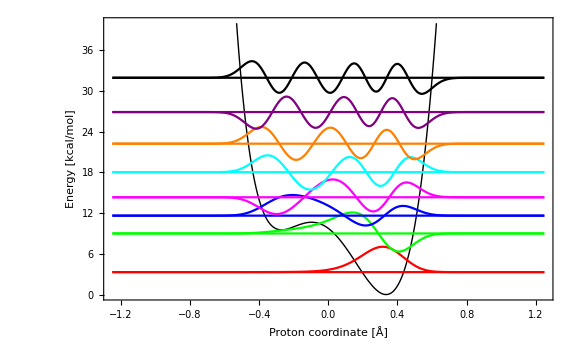

```mathematica
wavelist=waveH257;
ListLinePlot[{Table[{wavelist[[1,2]][[i,1]],wavelist[[1,2]][[i,2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]+25*wavelist[[1,3,1]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]+25*wavelist[[1,3,2]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]+25*wavelist[[1,3,3]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]+25*wavelist[[1,3,4]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]+25*wavelist[[1,3,5]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]+25*wavelist[[1,3,6]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[7]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[7]]+25*wavelist[[1,3,7]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[8]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[8]]+25*wavelist[[1,3,8]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}]},PlotRange->{0,40},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange,Purple,Purple,Black,Black}]
```

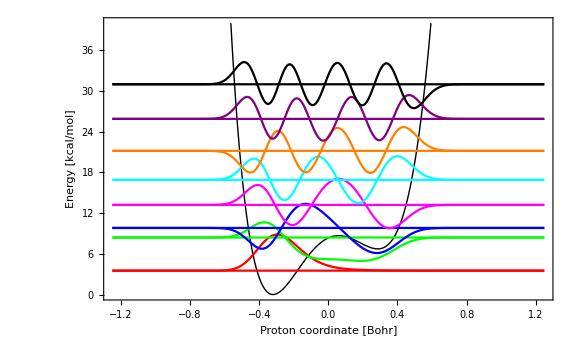

```mathematica
wavelist=waveH257;
ListLinePlot[{Table[{wavelist[[2,2]][[i,1]],wavelist[[2,2]][[i,2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]+25*wavelist[[2,3,1]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]+25*wavelist[[2,3,2]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]+25*wavelist[[2,3,3]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]+25*wavelist[[2,3,4]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]+25*wavelist[[2,3,5]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]+25*wavelist[[2,3,6]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[7]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[7]]+25*wavelist[[2,3,7]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[8]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[8]]+25*wavelist[[2,3,8]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}]},PlotRange->{0,40},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange,Purple,Purple,Black,Black}]
```

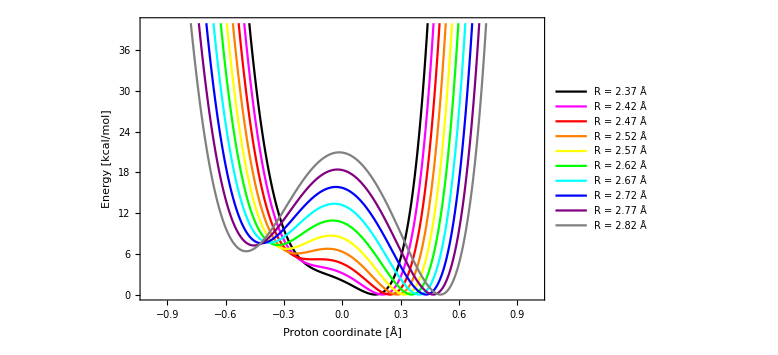

```mathematica
ListLinePlot[{Table[{-waveH237[[2,2]][[i,1]],waveH237[[2,2]][[i,2]]},{i,1,Length[waveH237[[1,3,1]]]}],
Table[{-waveH242[[2,2]][[i,1]],waveH242[[2,2]][[i,2]]},{i,1,Length[waveH242[[1,3,1]]]}],
Table[{-waveH247[[2,2]][[i,1]],waveH247[[2,2]][[i,2]]},{i,1,Length[waveH247[[1,3,1]]]}],Table[{-waveH252[[2,2]][[i,1]],waveH252[[2,2]][[i,2]]},{i,1,Length[waveH252[[1,3,1]]]}],Table[{-waveH257[[2,2]][[i,1]],waveH257[[2,2]][[i,2]]},{i,1,Length[waveH257[[1,3,1]]]}],Table[{-waveH262[[2,2]][[i,1]],waveH262[[2,2]][[i,2]]},{i,1,Length[waveH262[[1,3,1]]]}],Table[{-waveH267[[2,2]][[i,1]],waveH267[[2,2]][[i,2]]},{i,1,Length[waveH267[[1,3,1]]]}],Table[{-waveH272[[2,2]][[i,1]],waveH272[[2,2]][[i,2]]},{i,1,Length[waveH272[[1,3,1]]]}],Table[{-waveH277[[2,2]][[i,1]],waveH277[[2,2]][[i,2]]},{i,1,Length[waveH277[[1,3,1]]]}],Table[{-waveH282[[2,2]][[i,1]],waveH282[[2,2]][[i,2]]},{i,1,Length[waveH282[[1,3,1]]]}]},PlotRange->{{-1,1},{0,40}} ,ImageSize->Large,BaseStyle->{FontSize->20},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},FrameStyle->{Black,FontSize->20},LabelStyle-> {Black,FontSize->20},PlotStyle->{Black,Magenta,Red,Orange,Yellow,Green,Cyan,Blue,Purple,Gray},PlotLegends->Placed[{"R = 2.37 Å","R = 2.42 Å","R = 2.47 Å","R = 2.52 Å","R = 2.57 Å","R = 2.62 Å","R = 2.67 Å","R = 2.72 Å","R = 2.77 Å","R = 2.82 Å"},Right]]
```

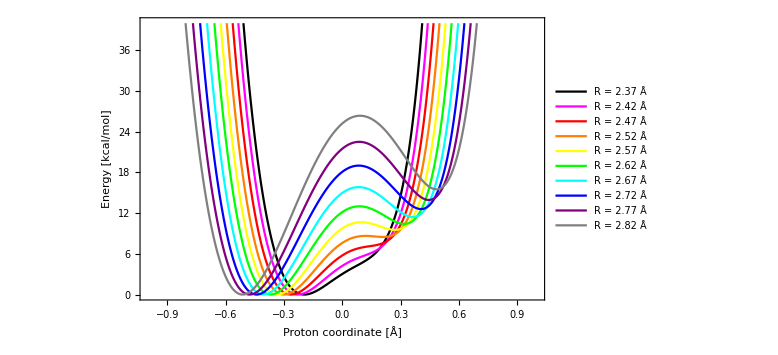

```mathematica
ListLinePlot[{Table[{-waveH237[[1,2]][[i,1]],waveH237[[1,2]][[i,2]]},{i,1,Length[waveH237[[1,3,1]]]}],
Table[{-waveH242[[1,2]][[i,1]],waveH242[[1,2]][[i,2]]},{i,1,Length[waveH242[[1,3,1]]]}],
Table[{-waveH247[[1,2]][[i,1]],waveH247[[1,2]][[i,2]]},{i,1,Length[waveH247[[1,3,1]]]}],Table[{-waveH252[[1,2]][[i,1]],waveH252[[1,2]][[i,2]]},{i,1,Length[waveH252[[1,3,1]]]}],Table[{-waveH257[[1,2]][[i,1]],waveH257[[1,2]][[i,2]]},{i,1,Length[waveH257[[1,3,1]]]}],Table[{-waveH262[[1,2]][[i,1]],waveH262[[1,2]][[i,2]]},{i,1,Length[waveH262[[1,3,1]]]}],Table[{-waveH267[[1,2]][[i,1]],waveH267[[1,2]][[i,2]]},{i,1,Length[waveH267[[1,3,1]]]}],Table[{-waveH272[[1,2]][[i,1]],waveH272[[1,2]][[i,2]]},{i,1,Length[waveH272[[1,3,1]]]}],Table[{-waveH277[[1,2]][[i,1]],waveH277[[1,2]][[i,2]]},{i,1,Length[waveH277[[1,3,1]]]}],Table[{-waveH282[[1,2]][[i,1]],waveH282[[1,2]][[i,2]]},{i,1,Length[waveH282[[1,3,1]]]}]},PlotRange->{{-1,1},{0,40}} ,ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},FrameStyle->{Black,FontSize->20},LabelStyle-> {Black,FontSize->20},PlotStyle->{Black,Magenta,Red,Orange,Yellow,Green,Cyan,Blue,Purple,Gray},PlotLegends->Placed[{"R = 2.37 Å","R = 2.42 Å","R = 2.47 Å","R = 2.52 Å","R = 2.57 Å","R = 2.62 Å","R = 2.67 Å","R = 2.72 Å","R = 2.77 Å","R = 2.82 Å"},Right]]
```

## Functions for MS-CPET (k_f) and recombination (k_r) total rate constants - Proton and Deuterium

```mathematica
TotalRateRfixedFGH[waveH257,Vel,dGr,λs,TT,2,10]
```

6.20585×10^7

```mathematica
TableRateRfixedFGH[waveH257,Vel,-2.58 ev2kcal,λs,TT,2,11]
```

ΔG_00=-59.5kcal/mol; λ=24.67kcal/mol |  |  |  |  |  |  | 
μ | ν | P_μ | ΔG_μν | ΔG | S | exp(-βΔG) | %
0 | 0 | 9.99933e-1 |  -59.496 |   12.285 | 1.03244e-3 | 9.88465e-10 |     4.567×10^-6
0 | 1 | 9.99933e-1 |  -54.611 |    9.080 | 4.53486e-1 | 2.21155e-7 |     0.449
0 | 2 | 9.99933e-1 |  -53.202 |    8.245 | 4.23925e-1 | 9.04618e-7 |     1.716
0 | 3 | 9.99933e-1 |  -49.805 |    6.398 | 1.02768e-1 | 2.04174e-5 |     9.390
0 | 4 | 9.99933e-1 |  -46.113 |    4.657 | 1.72912e-2 | 3.86126e-4 |    29.879
0 | 5 | 9.99933e-1 |  -41.837 |    2.984 | 1.44597e-3 | 6.49553e-3 |    42.032
0 | 6 | 9.99933e-1 |  -37.124 |    1.570 | 4.99381e-5 | 7.06206e-2 |    15.782
0 | 7 | 9.99933e-1 |  -32.024 |    0.547 | 4.78141e-8 | 3.97044e-1 |     0.085
0 | 8 | 9.99933e-1 |  -26.577 |    0.037 | 1.40746e-7 | 9.40024e-1 |     0.592
0 | 9 | 9.99933e-1 |  -20.811 |    0.151 | 1.91397e-8 | 7.74706e-1 |     0.066
0 | 10 | 9.99933e-1 |  -14.752 |    0.998 | 3.67905e-10 | 1.85702e-1 |     0.000
0 | 11 | 9.99933e-1 |   -8.421 |    2.677 | 2.25969e-11 | 1.09111e-2 |     1.103×10^-6
1 | 0 | 6.66969e-5 |  -65.193 |   16.634 | 5.02726e-2 | 6.41813e-13 |     9.631×10^-12
1 | 1 | 6.66969e-5 |  -60.307 |   12.864 | 2.74447e-1 | 3.72026e-10 |     3.048×10^-8
1 | 2 | 6.66969e-5 |  -58.898 |   11.867 | 1.84564e-2 | 2.0025e-9 |     1.103×10^-8
1 | 3 | 6.66969e-5 |  -55.502 |    9.628 | 4.01083e-1 | 8.76048e-8 |     0.000
1 | 4 | 6.66969e-5 |  -51.810 |    7.460 | 2.10801e-1 | 3.40122e-6 |     0.000
1 | 5 | 6.66969e-5 |  -47.534 |    5.294 | 4.10168e-2 | 1.31636e-4 |     0.002
1 | 6 | 6.66969e-5 |  -42.821 |    3.336 | 3.78446e-3 | 3.58461e-3 |     0.004
1 | 7 | 6.66969e-5 |  -37.721 |    1.725 | 1.39031e-4 | 5.44375e-2 |     0.002
1 | 8 | 6.66969e-5 |  -32.274 |    0.585 | 2.35793e-7 | 3.72547e-1 |     0.000
1 | 9 | 6.66969e-5 |  -26.508 |    0.034 | 3.00099e-7 | 9.44147e-1 |     0.000
1 | 10 | 6.66969e-5 |  -20.449 |    0.181 | 3.72442e-8 | 7.36885e-1 |     8.192×10^-6
1 | 11 | 6.66969e-5 |  -14.117 |    1.129 | 4.21788e-10 | 1.48677e-1 |     1.872×10^-8
2 | 0 | 7.93384e-7 |  -67.819 |   18.859 | 6.77268e-1 | 1.49969e-14 |     3.606×10^-14
2 | 1 | 7.93384e-7 |  -62.933 |   14.830 | 1.87229e-2 | 1.34807e-11 |     8.962×10^-13
2 | 2 | 7.93384e-7 |  -61.524 |   13.758 | 1.16996e-1 | 8.23501e-11 |     3.421×10^-11
2 | 3 | 7.93384e-7 |  -58.127 |   11.338 | 2.56841e-2 | 4.88753e-9 |     4.457×10^-10
2 | 4 | 7.93384e-7 |  -54.436 |    8.974 | 1.14758e-1 | 2.64344e-7 |     1.077×10^-7
2 | 5 | 7.93384e-7 |  -50.159 |    6.580 | 4.06092e-2 | 1.50204e-5 |     2.166×10^-6
2 | 6 | 7.93384e-7 |  -45.447 |    4.372 | 5.61357e-3 | 6.24499e-4 |     0.000
2 | 7 | 7.93384e-7 |  -40.347 |    2.489 | 3.4365e-4 | 1.49929e-2 |     0.000
2 | 8 | 7.93384e-7 |  -34.899 |    1.059 | 5.12197e-6 | 1.67353e-1 |     3.044×10^-6
2 | 9 | 7.93384e-7 |  -29.134 |    0.201 | 1.10462e-7 | 7.11774e-1 |     2.792×10^-7
2 | 10 | 7.93384e-7 |  -23.075 |    0.026 | 5.54971e-8 | 9.57177e-1 |     1.886×10^-7
2 | 11 | 7.93384e-7 |  -16.743 |    0.637 | 1.88215e-9 | 3.41018e-1 |     2.279×10^-9

```mathematica
TableRateRfixedFGH[waveD257,Vel,dGr,λs,TT,9,9];
```

Recombination rate constant k_r:
(mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states)

```mathematica
krTotalH[dG_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,krH237,krH242,krH247,krH252,krH257,krH262,krH267,krH272,krH277,krH282,krH287,listkAH,krHR,krHtotal,krH,krHmax},

output=OptionValue[Output];

krH237=TotalRateRfixedFGH[waveH237,Vel,dG,λs,TT,mumax,numax];
krH242=TotalRateRfixedFGH[waveH242,Vel,dG,λs,TT,mumax,numax];
krH247=TotalRateRfixedFGH[waveH247,Vel,dG,λs,TT,mumax,numax];
krH252=TotalRateRfixedFGH[waveH252,Vel,dG,λs,TT,mumax,numax];
krH257=TotalRateRfixedFGH[waveH257,Vel,dG,λs,TT,mumax,numax];
krH262=TotalRateRfixedFGH[waveH262,Vel,dG,λs,TT,mumax,numax];
krH267=TotalRateRfixedFGH[waveH267,Vel,dG,λs,TT,mumax,numax];
krH272=TotalRateRfixedFGH[waveH272,Vel,dG,λs,TT,mumax,numax];
krH277=TotalRateRfixedFGH[waveH277,Vel,dG,λs,TT,mumax,numax];
krH282=TotalRateRfixedFGH[waveH282,Vel,dG,λs,TT,mumax,numax];
krH287=TotalRateRfixedFGH[waveH287,Vel,dG,λs,TT,mumax,numax];

listkAH={{R237,krH237},{R242,krH242},{R247,krH247},{R252,krH252},{R257,krH257},{R262,krH262},{R267,krH267},{R272,krH272},{R277,krH277},{R282,krH282},{R287,krH287}};

Off[InterpolatingFunction::dmval];
krHR=Interpolation[listkAH,InterpolationOrder->2];

krH[R_]:=If[krHR[R]<0,0,krHR[R]];

krHmax=FindMaximum[krH[x]Pav[x],{x,2.0,3.5}];
krHtotal=NIntegrate[krH[x]Pav[x],{x,0,∞}];

krHtotal
];
```

```mathematica
krTotalH[-31,2,11]
```

2.87543×10^13

```mathematica
krTotalHdetail[dG_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,krH237,krH242,krH247,krH252,krH257,krH262,krH267,krH272,krH277,krH282,krH287,listkAH,krHR,krHtotal,krH,krHmax},

output=OptionValue[Output];

krH237=TotalRateRfixedFGH[waveH237,Vel,dG,λs,TT,mumax,numax];
krH242=TotalRateRfixedFGH[waveH242,Vel,dG,λs,TT,mumax,numax];
krH247=TotalRateRfixedFGH[waveH247,Vel,dG,λs,TT,mumax,numax];
krH252=TotalRateRfixedFGH[waveH252,Vel,dG,λs,TT,mumax,numax];
krH257=TotalRateRfixedFGH[waveH257,Vel,dG,λs,TT,mumax,numax];
krH262=TotalRateRfixedFGH[waveH262,Vel,dG,λs,TT,mumax,numax];
krH267=TotalRateRfixedFGH[waveH267,Vel,dG,λs,TT,mumax,numax];
krH272=TotalRateRfixedFGH[waveH272,Vel,dG,λs,TT,mumax,numax];
krH277=TotalRateRfixedFGH[waveH277,Vel,dG,λs,TT,mumax,numax];
krH282=TotalRateRfixedFGH[waveH282,Vel,dG,λs,TT,mumax,numax];
krH287=TotalRateRfixedFGH[waveH287,Vel,dG,λs,TT,mumax,numax];

listkAH={{R237,krH237},{R242,krH242},{R247,krH247},{R252,krH252},{R257,krH257},{R262,krH262},{R267,krH267},{R272,krH272},{R277,krH277},{R282,krH282},{R287,krH287}};

Off[InterpolatingFunction::dmval];
krHR=Interpolation[listkAH,InterpolationOrder->2];

krH[R_]:=If[krHR[R]<0,0,krHR[R]];

krHmax=FindMaximum[krH[x]Pav[x],{x,2.0,3.5}];
krHtotal=NIntegrate[krH[x]Pav[x],{x,0,∞}];

If[output,Print["k_r^H(total) = ",krHtotal,"\nk_r^H(max) = ",krHmax⟦1⟧," s^-1","\nR_r(max) = ",krHmax⟦2,1,2⟧," Å"]];
krHtotal
listkAH
];
```

```mathematica
krTotalHdetail[dGc,2,11,Output-> True]
```

k_r^H(total) = 3.58044×10^12
k_r^H(max) = 2.06094×10^13 s^-1
R_r(max) = 2.57927 Å

{{8.46964×10^12,6.63016×10^24},{8.64866×10^12,8.03684×10^24},{8.82769×10^12,9.63048×10^24},{9.00671×10^12,1.13067×10^25},{9.18573×10^12,1.29921×10^25},{9.36475×10^12,1.46683×10^25},{9.54377×10^12,1.57681×10^25},{9.7228×10^12,1.5238×10^25},{9.90182×10^12,1.37914×10^25},{1.00808×10^13,1.0714×10^25},{1.02599×10^13,6.91189×10^24}}

```mathematica
krHplot[dG_,mumax_,numax_]:=Module[
{krH237,krH242,krH247,krH252,krH257,krH262,krH267,krH272,krH277,krH282,krH287,
kcH237,kcH242,kcH247,kcH252,kcH257,kcH262,kcH267,kcH272,kcH277,kcH282,kcH287,
listkAH,listkCH,krHR,kcHR,krHtotal,kcHtotal,krH,kcH,krHRplot,kcHRplot},

krH237=TotalRateRfixedFGH[waveH237,Vel,dG,λs,TT,mumax,numax];
krH242=TotalRateRfixedFGH[waveH242,Vel,dG,λs,TT,mumax,numax];
krH247=TotalRateRfixedFGH[waveH247,Vel,dG,λs,TT,mumax,numax];
krH252=TotalRateRfixedFGH[waveH252,Vel,dG,λs,TT,mumax,numax];
krH257=TotalRateRfixedFGH[waveH257,Vel,dG,λs,TT,mumax,numax];
krH262=TotalRateRfixedFGH[waveH262,Vel,dG,λs,TT,mumax,numax];
krH267=TotalRateRfixedFGH[waveH267,Vel,dG,λs,TT,mumax,numax];
krH272=TotalRateRfixedFGH[waveH272,Vel,dG,λs,TT,mumax,numax];
krH277=TotalRateRfixedFGH[waveH277,Vel,dG,λs,TT,mumax,numax];
krH282=TotalRateRfixedFGH[waveH282,Vel,dG,λs,TT,mumax,numax];
krH287=TotalRateRfixedFGH[waveH287,Vel,dG,λs,TT,mumax,numax];

listkAH={{R237,krH237},{R242,krH242},{R247,krH247},{R252,krH252},{R257,krH257},{R262,krH262},{R267,krH267},{R272,krH272},{R277,krH277},{R282,krH282},{R287,krH287}};
Print[listkAH];

Off[InterpolatingFunction::dmval];
krHR=Interpolation[listkAH,InterpolationOrder->2];

krH[R_]:=If[krHR[R]<0,0,krHR[R]];

krHRplot=Plot[krH[x],{x,2,4},ImageSize->Large];


Show[ListPlot[listkAH,ImageSize->Large],krHRplot,Axes->False,Frame->True,FrameLabel->{"R, Å","k_a^H (s^-1)"}]
];
```

```mathematica
krHplot[dGr,2,11,Output-> True]
```

krHplot[-64.1085,2,11,Output→True]

{{2.36553,5.23111×10^8},{2.41553,6.23139×10^8},{2.46553,7.23172×10^8},{2.51553,8.15302×10^8},{2.56553,8.94928×10^8},{2.61553,9.67894×10^8},{2.66553,9.29712×10^8},{2.71553,6.89208×10^8},{2.76553,4.35042×10^8},{2.81553,1.83018×10^8},{2.86553,5.0192×10^7}}

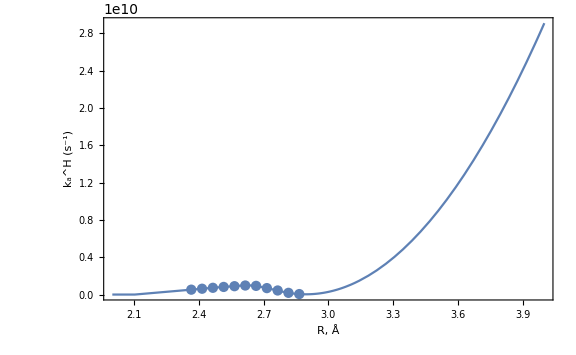

```mathematica
Show[krHplot[-60,7,7],PlotRange->All]
```

```mathematica
krTotalDdetail[dG_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,krD237,krD242,krD247,krD252,krD257,krD262,krD267,krD272,krD277,krD282,krD287,listkAD,krDR,krDtotal,krD,krDmax},

output=OptionValue[Output];

krD237=TotalRateRfixedFGH[waveD237,Vel,dG,λs,TT,mumax,numax];
krD242=TotalRateRfixedFGH[waveD242,Vel,dG,λs,TT,mumax,numax];
krD247=TotalRateRfixedFGH[waveD247,Vel,dG,λs,TT,mumax,numax];
krD252=TotalRateRfixedFGH[waveD252,Vel,dG,λs,TT,mumax,numax];
krD257=TotalRateRfixedFGH[waveD257,Vel,dG,λs,TT,mumax,numax];
krD262=TotalRateRfixedFGH[waveD262,Vel,dG,λs,TT,mumax,numax];
krD267=TotalRateRfixedFGH[waveD267,Vel,dG,λs,TT,mumax,numax];
krD272=TotalRateRfixedFGH[waveD272,Vel,dG,λs,TT,mumax,numax];
krD277=TotalRateRfixedFGH[waveD277,Vel,dG,λs,TT,mumax,numax];
krD282=TotalRateRfixedFGH[waveD282,Vel,dG,λs,TT,mumax,numax];
krD287=TotalRateRfixedFGH[waveD287,Vel,dG,λs,TT,mumax,numax];

listkAD={{R237,krD237},{R242,krD242},{R247,krD247},{R252,krD252},{R257,krD257},{R262,krD262},{R267,krD267},{R272,krD272},{R277,krD277},{R282,krD282},{R287,krD287}};

Off[InterpolatingFunction::dmval];
krDR=Interpolation[listkAD,InterpolationOrder->2];

krD[R_]:=If[krDR[R]<0,0,krDR[R]];

krDmax=FindMaximum[krD[x]Pav[x],{x,2.0,3.5}];
krDtotal=NIntegrate[krD[x]Pav[x],{x,0,∞}];

If[output,Print["k_r^D(total) = ",krDtotal,"\nk_r^D(max) = ",krDmax⟦1⟧," s^-1","\nR_r(max) = ",krDmax⟦2,1,2⟧," Å"]];
krDtotal
listkAD
];
```

```mathematica
krTotalDdetail[dGc,2,11,Output->True]
```

k_r^D(total) = 3.75659×10^12
k_r^D(max) = 2.16572×10^13 s^-1
R_r(max) = 2.57956 Å

{{8.88633×10^12,7.07581×10^24},{9.07416×10^12,8.69878×10^24},{9.26199×10^12,1.05021×10^25},{9.44982×10^12,1.24005×10^25},{9.63765×10^12,1.43105×10^25},{9.82548×10^12,1.62025×10^25},{1.00133×10^13,1.74432×10^25},{1.02011×10^13,1.68534×10^25},{1.0389×10^13,1.52605×10^25},{1.05768×10^13,1.18605×10^25},{1.07646×10^13,7.65445×10^24}}

```mathematica
krTotalD[dG_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,krD237,krD242,krD247,krD252,krD257,krD262,krD267,krD272,krD277,krD282,krD287,listkAD,krDR,krDtotal,krD,krDmax},

output=OptionValue[Output];

krD237=TotalRateRfixedFGH[waveD237,Vel,dG,λs,TT,mumax,numax];
krD242=TotalRateRfixedFGH[waveD242,Vel,dG,λs,TT,mumax,numax];
krD247=TotalRateRfixedFGH[waveD247,Vel,dG,λs,TT,mumax,numax];
krD252=TotalRateRfixedFGH[waveD252,Vel,dG,λs,TT,mumax,numax];
krD257=TotalRateRfixedFGH[waveD257,Vel,dG,λs,TT,mumax,numax];
krD262=TotalRateRfixedFGH[waveD262,Vel,dG,λs,TT,mumax,numax];
krD267=TotalRateRfixedFGH[waveD267,Vel,dG,λs,TT,mumax,numax];
krD272=TotalRateRfixedFGH[waveD272,Vel,dG,λs,TT,mumax,numax];
krD277=TotalRateRfixedFGH[waveD277,Vel,dG,λs,TT,mumax,numax];
krD282=TotalRateRfixedFGH[waveD282,Vel,dG,λs,TT,mumax,numax];
krD287=TotalRateRfixedFGH[waveD287,Vel,dG,λs,TT,mumax,numax];

listkAD={{R237,krD237},{R242,krD242},{R247,krD247},{R252,krD252},{R257,krD257},{R262,krD262},{R267,krD267},{R272,krD272},{R277,krD277},{R282,krD282},{R287,krD287}};

Off[InterpolatingFunction::dmval];
krDR=Interpolation[listkAD,InterpolationOrder->2];

krD[R_]:=If[krDR[R]<0,0,krDR[R]];

krDmax=FindMaximum[krD[x]Pav[x],{x,2.0,3.5}];
krDtotal=NIntegrate[krD[x]Pav[x],{x,0,∞}];

krDtotal
];
```

```mathematica
krTotalD[dE,2,11]
```

2.3652×10^11

```mathematica
krHdGPlot[dGmin_,dGmax_,δ_,mumax_,numax_]:=Module[
{dG,krHTable,krHdG,krHdGplot},

krHTable=Table[{-dG,krTotalH[dG,mumax,numax]},{dG,dGmin,dGmax,(dGmax-dGmin)/δ}];

Off[InterpolatingFunction::dmval];
krHdG=Interpolation[krHTable,InterpolationOrder->1];

Show[ListLogPlot[krHdG,ImageSize->Large,Axes->False,Frame->True,FrameLabel->{"-ΔG° (kcal/mol)","k_(CPET - CR) (s^-1)"},PlotStyle-> Black,FrameStyle-> {Black,FontSize-> 24},LabelStyle-> {Black,FontSize-> 24}
]
]
];
```

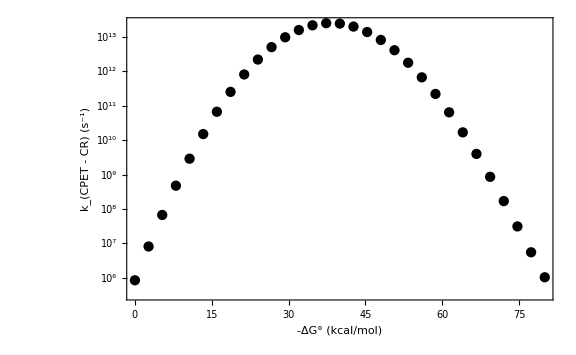

```mathematica
p1=krHdGPlot[-80,0,30,2,11]
```

```mathematica
-2.11 ev2kcal
```

-48.6579

```mathematica
krKIEdGPlot[dGmin_,dGmax_,δ_,mumax_,numax_]:=Module[
{dG,krKIETable,krKIEdG,krKIEdGplot},

krKIETable=Table[{dG,krTotalH[dG,mumax,numax]/krTotalD[dG,mumax,numax]},{dG,dGmin,dGmax,(dGmax-dGmin)/δ}];

Off[InterpolatingFunction::dmval];
krKIEdG=Interpolation[krKIETable,InterpolationOrder->1];

(*krKIEdG[dG_]:=If[krKIEdG[dG]<0,0,krKIEdG[dG]];

krKIEdGplot=Plot[krKIEdG[x],{x,dGmin,dGmax},ImageSize->Large];*)

Show[ListLinePlot[krKIEdG,ImageSize->Large],(*krKIEdGplot,*)Axes->False,Frame->True,FrameLabel->{"ΔG°","KIE"},FontSize->24]
];
```

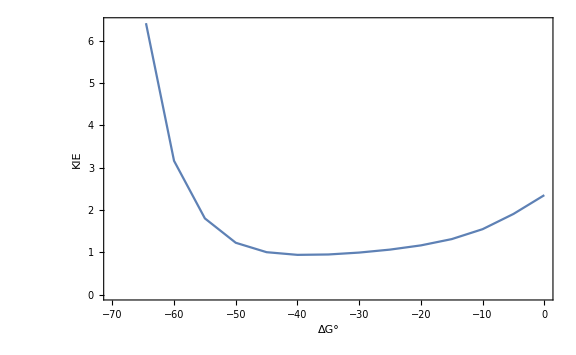

```mathematica
krKIEdGPlot[-70,0,14,2,11]
```

## Morse potentials for MIR

```mathematica
DEMorseL=100;
BetaMorseL=1.96/a2bohr;
DEMorseR=100;
BetaMorseR=2.16/a2bohr;
xminL=0.333577712610000;
xminR=-0.321358748778000;
deq=0.65;
xlminL=-0.270039100684000;
xlminR=0.284701857283000;
dEL=9.537039309917027;
dER=6.730442431164020;
Rm237=2.37;
Rm242=2.42;
Rm247=2.47;
Rm252=2.52;
Rm257=2.57;
Rm262=2.62;
Rm267=2.67;
Rm272=2.72;
Rm277=2.77;
Rm282=2.82;
Rm287=2.87;
```

```mathematica
deq
```

0.65

```mathematica
ListLinePlot[{Table[{-waveH257[[1,2]][[i,1]],waveH257[[1,2]][[i,2]]},{i,1,Length[waveH257[[1,3,1]]]}]},PlotRange->{{-1,1},{0,40}} ,ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},FrameStyle->{Black,FontSize->20},LabelStyle-> {Black,FontSize->20},PlotStyle->{Black}]
```

-Graphics-

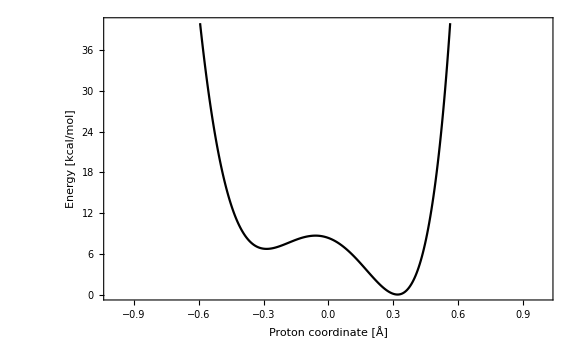

```mathematica
ListLinePlot[{Table[{-waveH257[[2,2]][[i,1]],waveH257[[2,2]][[i,2]]},{i,1,Length[waveH257[[2,3,1]]]}]},PlotRange->{{-1,1},{0,40}} ,ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},FrameStyle->{Black,FontSize->20},LabelStyle-> {Black,FontSize->20},PlotStyle->{Black}]
```

```mathematica
BetaMorse[ω_,DE_,μ_]:=ω cm2au√(μ/(2(DE/au2kcal)));
```

```mathematica
BetaMorse[3300,100,MassH*Dalton]/bohr2a
```

2.15664932

```mathematica
U1Left[Beta1_,DEA1_,x_]:=DEA1 kcal2au(1-Exp[Beta1*(-x)])^2;
U1Right[Beta1_,DEA1_,x_]:=DEA1 kcal2au(1-Exp[-Beta1*(-x)])^2;
MorseEnergy[n_,Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,betaa,Lambda,mu},
	DEA=DE*kcal2au;
betaa=Beta/a2bohr;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*betaa);
	au2kcal*hbar*((n+1/2)-1/(2*Lambda)*(n+1/2)^2)*Sqrt[(2*DEA*betaa^2)/mu]
];
NMorseOverlap[DE1_,Beta1_,DE2_,Beta2_,nu1_,nu2_,d_,OptionsPattern[{M->MassH}]]:=Module[{Mass,mu,DE1A,DE2A,Beta1A,Beta2A,X,integrand},Mass=OptionValue[M];
mu=Mass*Dalton;
DE1A=DE1*kcal2au;
DE2A=DE2*kcal2au;
Beta1A=Beta1/a2bohr;
Beta2A=Beta2/a2bohr;
integrand[x_]:=MorseWavefunctionLeft[nu1,Beta1A,DE1,x,M->Mass]*MorseWavefunctionRight[nu2,Beta2A,DE2,x-d,M->Mass];
NIntegrate[integrand[X],{X,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False]];
MorseBound[Beta_,DE_,OptionsPattern[{M->MassH}]]:=Module[{DEA,BetaA,Lambda,mu},
	DEA=DE*kcal2au;
BetaA=Beta/a2bohr;
	mu=OptionValue[M]*Dalton;
	Lambda=Sqrt[2*mu*DEA]/(hbar*Beta);
	IntegerPart[Lambda-1/2]
];
```

```mathematica
MorseBound[2.16/a2bohr,100,M-> MassH]
```

20

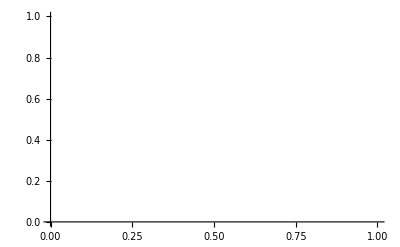

```mathematica
Show[ListLinePlot[{Table[{-waveH257[[1,2]][[i,1]],waveH257[[1,2]][[i,2]]},{i,1,Length[waveH257[[1,3,1]]]}]},PlotStyle->{Black},PlotRange->{{-0.8,0.8},{0,60}}],Plot[U1Left[2.16,100,x+xminL]au2kcal,{x,-5,5},PlotStyle->{Blue}]]
```

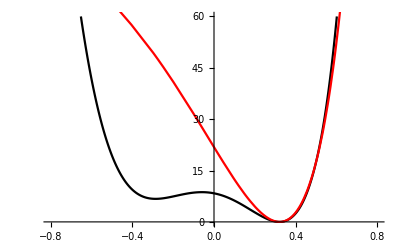

```mathematica
Show[ListLinePlot[{Table[{-waveH257[[2,2]][[i,1]],waveH257[[2,2]][[i,2]]},{i,1,Length[waveH257[[2,3,1]]]}]},PlotStyle->{Black},PlotRange->{{-0.8,0.8},{0,60}}],Plot[U1Right[1.96,100,x+xminR]au2kcal,{x,-5,5},PlotStyle->{Red}]]
```

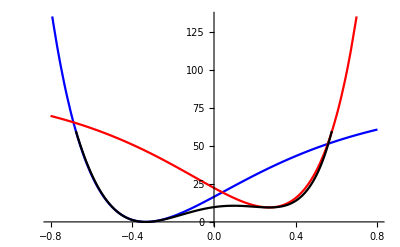

```mathematica
Show[Plot[{U1Left[1.82,80,x+xminL]au2kcal,U1Right[1.9,80,x+xlminL]au2kcal+dEL},{x,-0.8,0.8},PlotStyle->{Blue,Red}],ListLinePlot[{Table[{-waveH257[[1,2]][[i,1]],waveH257[[1,2]][[i,2]]},{i,1,Length[waveH257[[1,3,1]]]}]},PlotStyle->{Black},PlotRange->{{-1.0,1.0},{0,60}}]]
```

```mathematica
NMorseOverlap[100,BetaMorseL,100,BetaMorseR,0,0,0.65a2bohr,M->MassH]
```

0.0154665

```mathematica
BetaMorseL/a2bohr
```

0.548855

```mathematica
PartialRateRfixedMorse[1,0,25,100,BetaMorseL,100,BetaMorseR,0.65 a2bohr,298.15,0,0,M->MassH]
```

190350.

```mathematica
kMorseH[dG_,λ_,DE1_,Beta1_,DE2_,Beta2_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,krH237,krH242,krH247,krH252,krH257,krH262,krH267,krH272,krH277,krH282,krH287,listkAH,krHR,krHtotal,krH,krHmax},
output=OptionValue[Output];
krH237=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.2)a2bohr,TT,mumax,numax];
krH242=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.15)a2bohr,TT,mumax,numax];
krH247=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.1)a2bohr,TT,mumax,numax];
krH252=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.05)a2bohr,TT,mumax,numax];
krH257=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.0)a2bohr,TT,mumax,numax];
krH262=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.05)a2bohr,TT,mumax,numax];
krH267=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.1)a2bohr,TT,mumax,numax];
krH272=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.15)a2bohr,TT,mumax,numax];
krH277=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.2)a2bohr,TT,mumax,numax];
krH282=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.25)a2bohr,TT,mumax,numax];
krH287=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.3)a2bohr,TT,mumax,numax];

listkAH={{Rm237,krH237},{Rm242,krH242},{Rm247,krH247},{Rm252,krH252},{Rm257,krH257},{Rm262,krH262},{Rm267,krH267},{Rm272,krH272},{Rm277,krH277},{Rm282,krH282},{Rm287,krH287}};

Off[InterpolatingFunction::dmval];
krHR=Interpolation[listkAH,InterpolationOrder->3];
krH[R_]:=Piecewise[{{krHR[R],R<2.87},{0,R>2.87}}];
(*krH[R_]:=If[krHR[R]<0,0,krHR[R]];*)
krHmax=FindMaximum[krH[x]Pav[x],{x,2.0,3.5}];
krHtotal=NIntegrate[krH[x]Pav[x],{x,0,∞}];
If[output,Print["k_r^H(total) = ",krHtotal,"\nk_r^H(max) = ",krHmax⟦1⟧," s^-1","\nR_r(max) = ",krHmax⟦2,1,2⟧," Å"]];
krHtotal
(*listkAH*)
];
kMorseD[dG_,λ_,DE1_,Beta1_,DE2_,Beta2_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,krH237,krH242,krH247,krH252,krH257,krH262,krH267,krH272,krH277,krH282,krH287,listkAH,krHR,krHtotal,krH,krHmax},
output=OptionValue[Output];
krH237=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.2)a2bohr,TT,mumax,numax,M-> MassD];
krH242=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.15)a2bohr,TT,mumax,numax,M-> MassD];
krH247=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.1)a2bohr,TT,mumax,numax,M-> MassD];
krH252=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.05)a2bohr,TT,mumax,numax,M-> MassD];
krH257=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.0)a2bohr,TT,mumax,numax,M-> MassD];
krH262=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.05)a2bohr,TT,mumax,numax,M-> MassD];
krH267=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.1)a2bohr,TT,mumax,numax,M-> MassD];
krH272=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.15)a2bohr,TT,mumax,numax,M-> MassD];
krH277=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.2)a2bohr,TT,mumax,numax,M-> MassD];
krH282=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.25)a2bohr,TT,mumax,numax,M-> MassD];
krH287=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.3)a2bohr,TT,mumax,numax,M-> MassD];
listkAH={{Rm237,krH237},{Rm242,krH242},{Rm247,krH247},{Rm252,krH252},{Rm257,krH257},{Rm262,krH262},{Rm267,krH267},{Rm272,krH272},{Rm277,krH277},{Rm282,krH282},{Rm287,krH287}};
Off[InterpolatingFunction::dmval];
krHR=Interpolation[listkAH,InterpolationOrder->2];
krH[R_]:=If[krHR[R]<0,0,krHR[R]];
krHmax=FindMaximum[krH[x]Pav[x],{x,2.0,3.5}];
krHtotal=NIntegrate[krH[x]Pav[x],{x,0,∞}];
If[output,Print["k_r^D(total) = ",krHtotal,"\nk_r^D(max) = ",krHmax⟦1⟧," s^-1","\nR_r(max) = ",krHmax⟦2,1,2⟧," Å"]];
krHtotal
(*listkAH*)
];
```

```mathematica
1.2 ev2kcal
```

27.6727

```mathematica
dG=0;
λ=25;
DE1=DEMorseL;DE2=DEMorseR;
Beta1=BetaMorseL;Beta2=BetaMorseR;
mumax=3;
numax=12;
krH237=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.2)a2bohr,TT,mumax,numax];
krH242=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.15)a2bohr,TT,mumax,numax];
krH247=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.1)a2bohr,TT,mumax,numax];
krH252=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.05)a2bohr,TT,mumax,numax];
krH257=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq-0.0)a2bohr,TT,mumax,numax];
krH262=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.05)a2bohr,TT,mumax,numax];
krH267=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.1)a2bohr,TT,mumax,numax];
krH272=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.15)a2bohr,TT,mumax,numax];
krH277=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.2)a2bohr,TT,mumax,numax];
krH282=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.25)a2bohr,TT,mumax,numax];
krH287=TotalRateRfixedMorse[Vel,dG,λ,DE1,Beta1,DE2,Beta2,(deq+0.3)a2bohr,TT,mumax,numax];
listkAH={{Rm237,krH237},{Rm242,krH242},{Rm247,krH247},{Rm252,krH252},{Rm257,krH257},{Rm262,krH262},{Rm267,krH267},{Rm272,krH272},{Rm277,krH277},{Rm282,krH282},{Rm287,krH287}};
Off[InterpolatingFunction::dmval];
krHR=Interpolation[listkAH,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
listkAH//TableForm
```

2.37 | 1.78355×10^7
2.42 | 7.13311×10^6
2.47 | 2.61327×10^6
2.52 | 879766.
2.57 | 273014.
2.62 | 78341.
2.67 | 20851.
2.72 | 5163.49
2.77 | 1193.37
2.82 | 258.201
2.87 | 52.4585

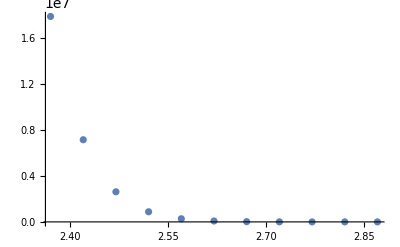

```mathematica
ListPlot[listkAH]
```

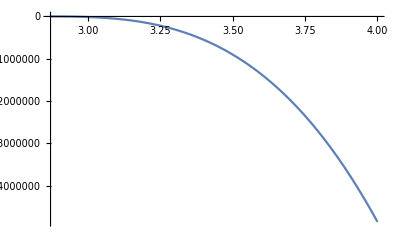

```mathematica
Plot[krHR[x],{x,2.87,4.}]
```

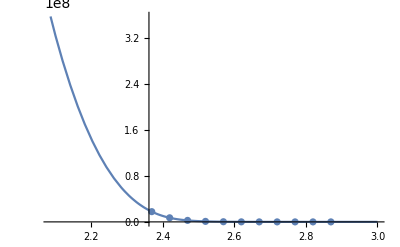

```mathematica
Show[ListPlot[listkAH],Plot[krHR[x],{x,2.,3.}],PlotRange->All]
```

```mathematica
kMorseH[0,25,DEMorseL,BetaMorseL,DEMorseR,BetaMorseR,2,14,Output->True]
```

k_r^H(total) = 992976.
k_r^H(max) = 6.00702×10^6 s^-1
R_r(max) = 2.4633 Å

992976.

```mathematica
MorseConvH=Table[{ν,kMorseH[-70,25,DEMorseL,BetaMorseL,DEMorseR,BetaMorseR,2,ν]},{ν,7,15}]//TableForm
```

7 | 2.61705×10^11
8 | 8.02958×10^11
9 | 1.28966×10^12
10 | 1.44682×10^12
11 | 1.46916×10^12
12 | 1.47322×10^12
13 | 1.4738×10^12
14 | 1.47384×10^12
15 | 1.47385×10^12

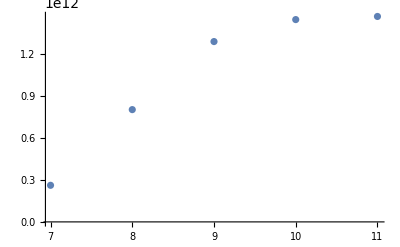

```mathematica
ListPlot[MorseConvH]
```

```mathematica
MorseConvD=Table[{ν,kMorseD[-60,25,DEMorseL,BetaMorseL,DEMorseR,BetaMorseR,2,ν]},{ν,1,15}]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in X$308208 in the region {{-∞,∞}}. NIntegrate obtained -0.00181345 and 6.01642×10^-8 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in X$308420 in the region {{-∞,∞}}. NIntegrate obtained 0.0175158 and 9.46521×10^-8 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in X$309295 in the region {{-∞,∞}}. NIntegrate obtained -0.0194785 and 1.87462×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

{{1,1018.83},{2,168893.},{3,1.20717×10^7},{4,4.23888×10^8},{5,7.90442×10^9},{6,8.27261×10^10},{7,5.08633×10^11},{8,1.92151×10^12},{9,4.70113×10^12},{10,7.98075×10^12},{11,1.03126×10^13},{12,1.13088×10^13},{13,1.15613×10^13},{14,1.15986×10^13},{15,1.16019×10^13}}

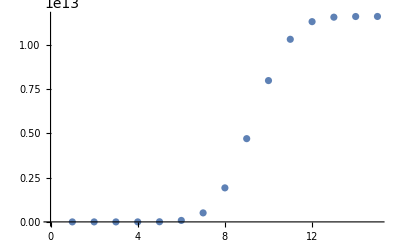

```mathematica
ListPlot[MorseConvD]
```

```mathematica
kMorseH[0,25,DEMorseL,BetaMorseL,DEMorseR,BetaMorseR,2,12]
```

1.02351×10^6

```mathematica
kMorseD[0,25,DEMorseL,BetaMorseL,DEMorseR,BetaMorseR,2,12]
```

175957.

```mathematica
(1.023507073704769*^6)/175957.0415670552
```

5.8168

```mathematica
{25,DEMorseL,BetaMorseL/bohr2a,DEMorseR,BetaMorseR/bohr2a}
```

{25,100,1.96,100,2.16}

```mathematica
kMorseHTable=Table[{ddG,kMorseH[-ddG,25,DEMorseL,BetaMorseL,DEMorseR,BetaMorseR,2,10]},{ddG,0,60,3}];
```

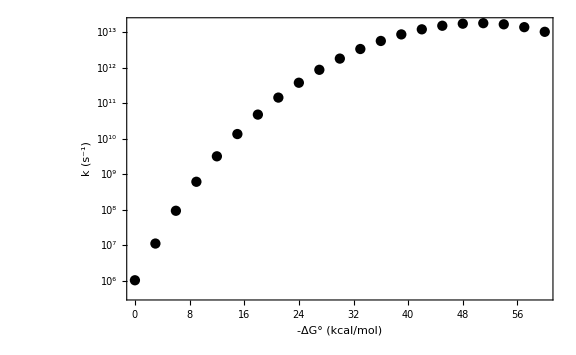

```mathematica
pM=ListLogPlot[kMorseHTable,ImageSize->Large,Axes->False,Frame->True,FrameLabel->{"-ΔG° (kcal/mol)","k (s^-1)"},PlotStyle-> Black,FrameStyle-> {Black,FontSize-> 24},LabelStyle-> {Black,FontSize-> 24}]
```

```mathematica
kMorseDTable=Table[{ddG,kMorseD[-ddG,25,DEMorseL,BetaMorseL,DEMorseR,BetaMorseR,2,14]},{ddG,0,60,3}];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in X$1095650 in the region {{-∞,∞}}. NIntegrate obtained -0.00113616 and 2.28078×10^-8 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in X$1095684 in the region {{-∞,∞}}. NIntegrate obtained 0.00065792 and 3.429×10^-7 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in X$1095898 in the region {{-∞,∞}}. NIntegrate obtained 0.0151771 and 6.42639×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

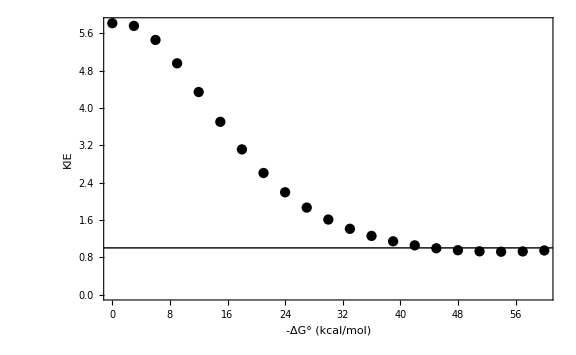

```mathematica
pMKIE=Show[ListPlot[Table[{kMorseHTable⟦i⟧⟦1⟧,kMorseHTable⟦i⟧⟦2⟧/kMorseDTable⟦i⟧⟦2⟧},{i,1,Length[kMorseHTable]}],ImageSize->Large,Axes->False,Frame->True,FrameLabel->{"-ΔG° (kcal/mol)","KIE"},PlotStyle-> Black,FrameStyle-> {Black,FontSize-> 24},LabelStyle-> {Black,FontSize-> 24}],Plot[1,{x,-5,65},PlotStyle->{Black,Thick}]]
```

```mathematica
Show[pMKIE]
```

```mathematica
λm
```

32.2849

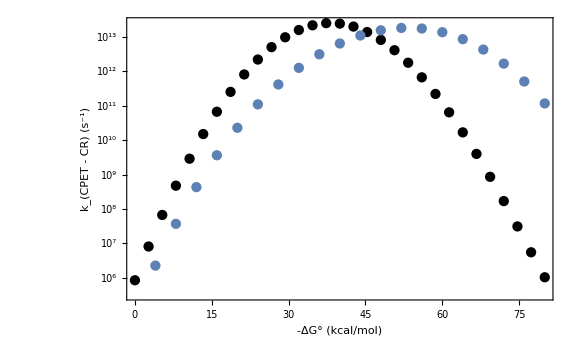

```mathematica
Show[p1,pM]
```

```mathematica
TableRateRfixedMorse[1,-60,λm,80,1.82/a2bohr,80,2.2/a2bohr,deq,TT,2,10,M-> MassH]
```

Isotope: 1.01amu; ΔG_00=-60kcal/mol; λ=32.28kcal/mol |  |  |  |  |  |  | 
μ | ν | P_μ | ΔG_μν | ΔG | S | exp(-βΔG) | %
0 | 0 | 9.97992e-1 |  -60.000 |    5.948 | 1.45711e-1 | 4.36589e-5 |     0.029
0 | 1 | 9.97992e-1 |  -55.574 |    4.200 | 3.20658e-1 | 8.34386e-4 |     1.203
0 | 2 | 9.97992e-1 |  -51.278 |    2.793 | 3.26146e-1 | 8.96242e-3 |    13.143
0 | 3 | 9.97992e-1 |  -47.112 |    1.702 | 1.67635e-1 | 5.6523e-2 |    42.602
0 | 4 | 9.97992e-1 |  -43.075 |    0.902 | 3.78437e-2 | 2.18359e-1 |    37.154
0 | 5 | 9.97992e-1 |  -39.168 |    0.367 | 1.55768e-3 | 5.38386e-1 |     3.771
0 | 6 | 9.97992e-1 |  -35.391 |    0.075 | 2.87035e-4 | 8.81562e-1 |     1.138
0 | 7 | 9.97992e-1 |  -31.743 |    0.002 | 1.5265e-4 | 9.96169e-1 |     0.684
0 | 8 | 9.97992e-1 |  -28.225 |    0.128 | 1.07988e-6 | 8.06208e-1 |     0.004
0 | 9 | 9.97992e-1 |  -24.837 |    0.430 | 7.53736e-6 | 4.84323e-1 |     0.016
0 | 10 | 9.97992e-1 |  -21.578 |    0.888 | 5.55593e-8 | 2.23544e-1 |     0.000
1 | 0 | 2.00332e-3 |  -63.680 |    7.632 | 3.71782e-1 | 2.54343e-6 |     8.534×10^-6
1 | 1 | 2.00332e-3 |  -59.254 |    5.632 | 9.25761e-2 | 7.4405e-5 |     0.000
1 | 2 | 2.00332e-3 |  -54.958 |    3.981 | 3.27912e-2 | 1.20817e-3 |     0.000
1 | 3 | 2.00332e-3 |  -50.792 |    2.652 | 2.48841e-1 | 1.13758e-2 |     0.026
1 | 4 | 2.00332e-3 |  -46.755 |    1.621 | 2.07869e-1 | 6.47976e-2 |     0.122
1 | 5 | 2.00332e-3 |  -42.848 |    0.864 | 4.40775e-2 | 2.32646e-1 |     0.093
1 | 6 | 2.00332e-3 |  -39.070 |    0.357 | 5.6643e-5 | 5.47836e-1 |     0.000
1 | 7 | 2.00332e-3 |  -35.423 |    0.076 | 1.78414e-3 | 8.79241e-1 |     0.014
1 | 8 | 2.00332e-3 |  -31.905 |    0.001 | 1.25786e-4 | 9.98116e-1 |     0.001
1 | 9 | 2.00332e-3 |  -28.517 |    0.110 | 8.11502e-5 | 8.30632e-1 |     0.001
1 | 10 | 2.00332e-3 |  -25.258 |    0.382 | 7.53678e-6 | 5.24516e-1 |     0.000
2 | 0 | 4.67133e-6 |  -67.271 |    9.478 | 3.4859e-1 | 1.12808e-7 |     8.276×10^-10
2 | 1 | 4.67133e-6 |  -62.845 |    7.232 | 7.48404e-2 | 4.99978e-6 |     7.875×10^-9
2 | 2 | 4.67133e-6 |  -58.549 |    5.342 | 1.229e-1 | 1.21512e-4 |     3.143×10^-7
2 | 3 | 4.67133e-6 |  -54.383 |    3.781 | 2.8512e-3 | 1.69169e-3 |     1.015×10^-7
2 | 4 | 4.67133e-6 |  -50.346 |    2.526 | 2.25147e-1 | 1.40755e-2 |     0.000
2 | 5 | 4.67133e-6 |  -46.439 |    1.551 | 1.96524e-1 | 7.29254e-2 |     0.000
2 | 6 | 4.67133e-6 |  -42.662 |    0.834 | 2.30585e-2 | 2.44806e-1 |     0.000
2 | 7 | 4.67133e-6 |  -39.014 |    0.351 | 3.12303e-3 | 5.53327e-1 |     0.000
2 | 8 | 4.67133e-6 |  -35.496 |    0.080 | 2.65492e-3 | 8.73913e-1 |     0.000
2 | 9 | 4.67133e-6 |  -32.108 |    0.000 | 5.14259e-5 | 9.99591e-1 |     1.082×10^-6
2 | 10 | 4.67133e-6 |  -28.849 |    0.091 | 2.27253e-4 | 8.57058e-1 |     4.099×10^-6

## Double-well potential fit to CSS and GS

## Rate Convergence

```mathematica
KIEData=Table[{η,Log[10,kaHEPTtotal[η,m,5,Output->False]/kaDEPTtotal[η,m,5,Output->False]]},{η,η0-0.5,η0,0.05},{m,1,5}]
```

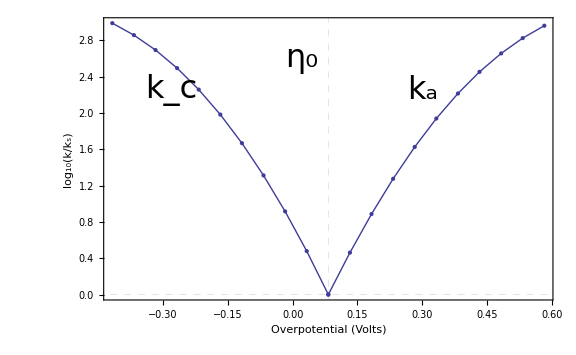

```mathematica
ListLinePlot[KIEData,
Mesh->All,
ImageSize->Large,
Axes->False,
Frame->True,
FrameLabel->{{Style["KIE",24,FontFamily->"Helvetica"],},{"Number of States",Style["Proton k_s = "<>ToString[ScientificForm[ks],FormatType->StandardForm]<>" sec^-1",32,FontFamily->"Helvetica"]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->24}
]
```

## Plots of the overlaps

obtained after finding main contributions to anodic and cathodic rate constants at dominant donor-acceptor distance

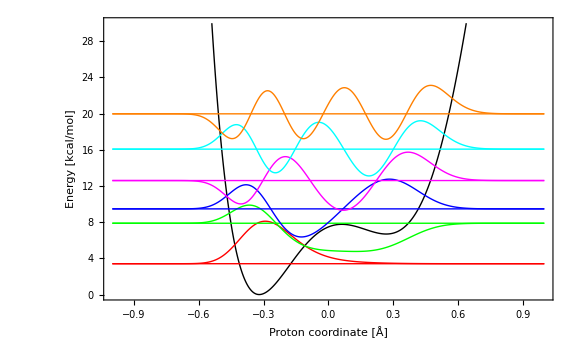

```mathematica
wavelist=waveH247;
ListLinePlot[{Table[{wavelist[[1,2]][[i,1]],wavelist[[1,2]][[i,2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]+50*wavelist[[1,3,1]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]+50*wavelist[[1,3,2]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]+50*wavelist[[1,3,3]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]+50*wavelist[[1,3,4]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]+50*wavelist[[1,3,5]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]+50*wavelist[[1,3,6]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}]},PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

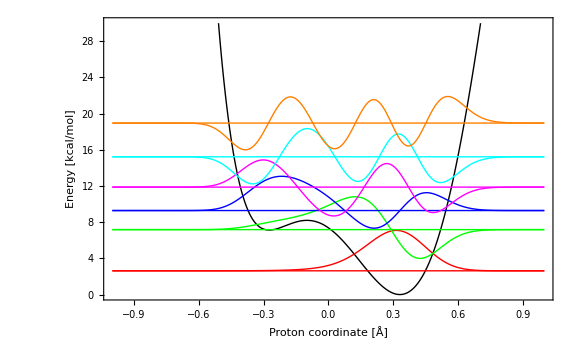

```mathematica
wavelist=waveH247;
ListLinePlot[{Table[{wavelist[[2,2]][[i,1]],wavelist[[2,2]][[i,2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]+50*wavelist[[2,3,1]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]+50*wavelist[[2,3,2]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]+50*wavelist[[2,3,3]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]+50*wavelist[[2,3,4]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]+50*wavelist[[2,3,5]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]+50*wavelist[[2,3,6]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}]},PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

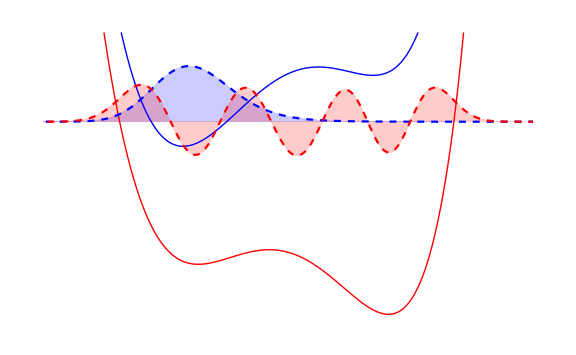

```mathematica
wavelist1=waveH257;
ListLinePlot[{
Table[{-wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,2⟧⟦i,2⟧-wavelist1⟦1,1⟧⟦1⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],Table[{-wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,2⟧⟦i,2⟧-wavelist1⟦2,1⟧⟦7⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{-wavelist1⟦1,2⟧⟦i,1⟧,50*wavelist1⟦1,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],
Table[{-wavelist1⟦2,2⟧⟦i,1⟧,50*wavelist1⟦2,3,7⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,4⟧]}]
},
PlotRange->{{-0.75,0.75},{-27,12}},
FrameTicks->{{{0,10,20,30},None},{{-0.50,0,0.50},None}},
ImageSize->Large,
BaseStyle->{FontFamily->"Helvetica",FontSize->16},
Axes->False,
Frame->False,
FrameLabel->{"Proton Coordinate [Å]","Energy [kcal/mol]"},
PlotStyle->{{Blue,Thick},{Red,Thick},{Blue,Dashed},{Red,Dashed}},
Filling->{{3-> Axis},{4-> Axis}}
]
```

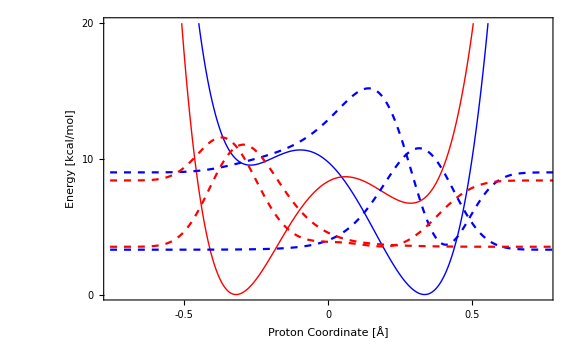

```mathematica
wavelist1=waveH257;
ListLinePlot[{
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦1⟧+50*wavelist1⟦1,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦2⟧+50*wavelist1⟦1,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,2⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦1⟧+50*wavelist1⟦2,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦2⟧+50*wavelist1⟦2,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,2⟧]}]
},
PlotRange->{{-0.75,0.75},{0,20}},
FrameTicks->{{{0,10,20,30},None},{{-0.50,0,0.50},None}},
ImageSize->Large,
BaseStyle->{FontFamily->"Helvetica",FontSize->16},
Axes->False,
Frame->True,
FrameLabel->{"Proton Coordinate [Å]","Energy [kcal/mol]"},
PlotStyle->{{Blue,Thick},{Red,Thick},{Blue,Dashed},{Blue,Dashed},{Red,Dashed},{Red,Dashed}}
]
```

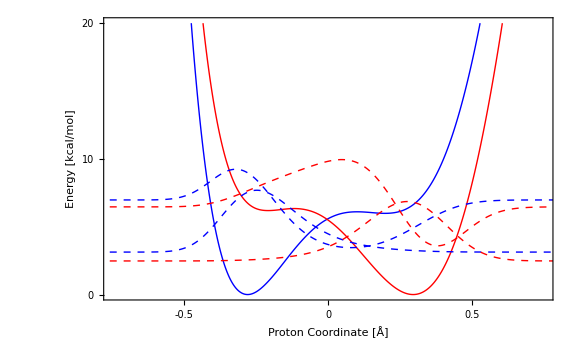

```mathematica
wavelist1=waveH242;
ListLinePlot[{
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦1⟧+50*wavelist1⟦1,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦2⟧+50*wavelist1⟦1,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,2⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦1⟧+50*wavelist1⟦2,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦2⟧+50*wavelist1⟦2,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,2⟧]}]
},
PlotRange->{{-0.75,0.75},{0,20}},
FrameTicks->{{{0,10,20,30},None},{{-0.50,0,0.50},None}},
ImageSize->Large,
BaseStyle->{FontFamily->"Helvetica",FontSize->16},
Axes->False,
Frame->True,
FrameLabel->{"Proton Coordinate [Å]","Energy [kcal/mol]"},
PlotStyle->{{Blue,Thick},{Red,Thick},{Blue,Dashed},{Blue,Dashed},{Red,Dashed},{Red,Dashed}}
]
```

## Marcus parabolas (kcal/mol)

```mathematica
GR[x_,i_]:=1/(4λs)(x+λs)^2+wavelist1⟦1,1⟧⟦i+1⟧;
GP[x_,i_]:=1/(4λs)(x-λs)^2+wavelist1⟦2,1⟧⟦i+1⟧;
```

```mathematica
wavelist1⟦2,1⟧⟦6⟧
```

21.1821

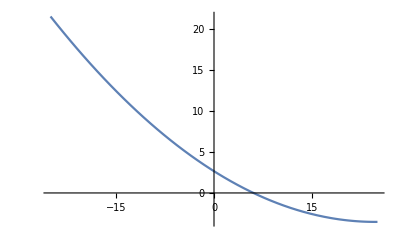

```mathematica
Plot[GP[x,1],{x,-25,25}]
```

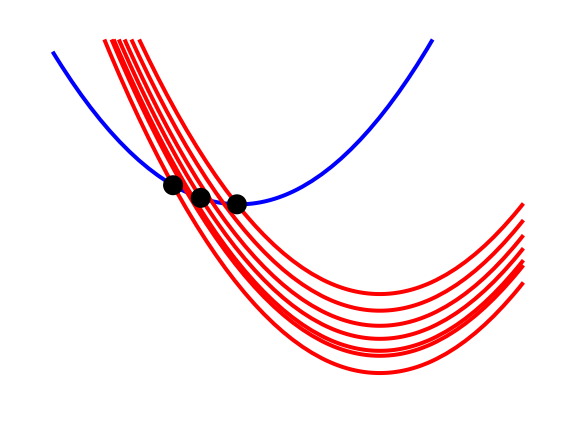

```mathematica
ΔG=-48;
x00=Solve[GR[x,0]==GP[x,0]+ΔG,x]⟦1,1,2⟧;
U00=GR[x00,0];
x03=Solve[GR[x,0]==GP[x,3]+ΔG,x]⟦1,1,2⟧;
U03=GR[x03,0];
x06=Solve[GR[x,0]==GP[x,6]+ΔG,x]⟦1,1,2⟧;
U06=GR[x06,0];
parabolas=Plot[{GR[x,0],GP[x,0]+ΔG,GP[x,1]+ΔG,GP[x,2]+ΔG,GP[x,3]+ΔG,GP[x,4]+ΔG,GP[x,5]+ΔG,GP[x,6]+ΔG},{x,-90,75},
PlotStyle->{{Blue,Thickness[0.005]},{Red,Thickness[0.005]},{Red,Thickness[0.005]},{Red,Thickness[0.005]},{Red,Thickness[0.005]},{Red,Thickness[0.005]},{Red,Thickness[0.005]},{Red,Thickness[0.005]}},
PlotRange->{-50,50},Axes->False,Frame->False,
ImageSize->Large,AspectRatio->0.75,
Epilog->{
Black,PointSize[0.025],Point[{x00,U00}],Point[{x06,U06}],Point[{x03,U03}],
Blue,FontSize->32,FontFamily->"Helvetica",Text["",{-43,10}],
Blue,FontSize->32,FontFamily->"Helvetica",Text["",{-29,20}],
Red,FontSize->32,FontFamily->"Helvetica",Text["",{44,10}],
Black,FontSize->28,FontFamily->"Helvetica",Text["",{8,7}],
Black,FontSize->28,FontFamily->"Helvetica",Text["",{0,12}]
}
]
```